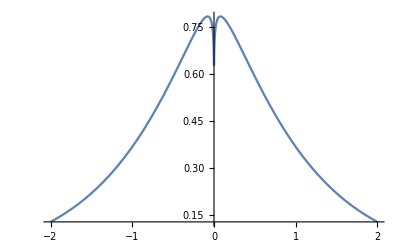

```mathematica
With[{c=1.07},Plot[Abs[x]^(c-1) Exp[-Abs[x]^c], {x,-2,2}]]
```

```mathematica
y [x_,loc_,scale_]:=(x-loc)/scale
```

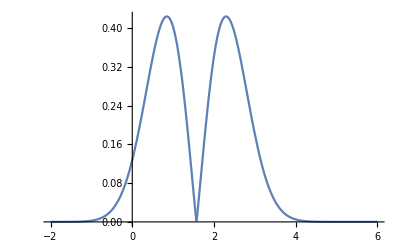

```mathematica
With[{c=2.06, loc = π/2, scale =1},Plot[Abs[(x-loc)/scale]^(c-1) Exp[-Abs[(x-loc)/scale]^c], {x,-2,6}]]
```